```mathematica
n=10
```

10

```mathematica
A=SparseArray[{
Band[{1,1}]->-β,
Band[{1,2}]->β
},{n+1,n+1}];
A[[1,1]]=0;
A=Normal[A];
MatrixForm[A];
```

```mathematica
ClearAll[p,sol,numsol,system,init]
```

```mathematica
ps[t_]:=Table[p[i][t],{i,1,n+1}]
```

```mathematica
system=D[ps[t],t]==A.ps[t];
p0=Array[0&,n+1];
p0[[n+1]]=1;
init=ps[0]==p0;
```

```mathematica
(*sol=DSolve[{system,init},ps[t],t];*)
```

```mathematica
numsol=NDSolveValue[{system,init},ps[t],{t,0,500}];
```

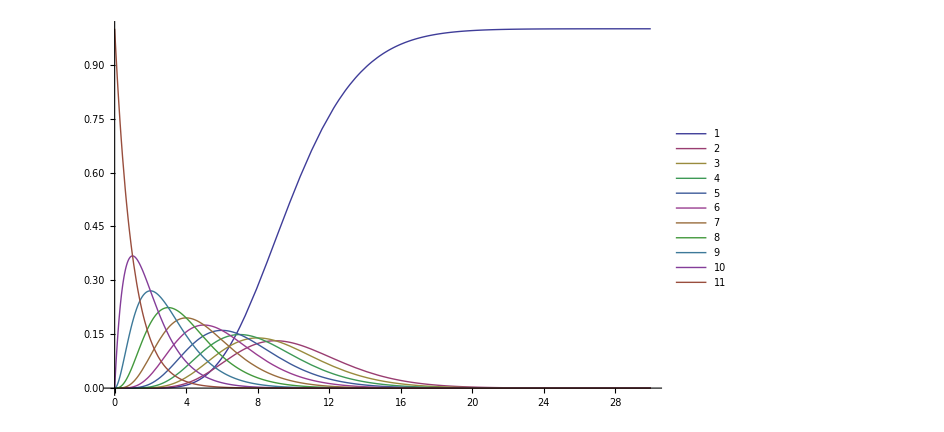

```mathematica
β=1;
(*p=Plot[ps[t]/.First@sol,{t,0,500},PlotRange->Full]*)
Plot[numsol,{t,0,30},PlotRange->Full,PlotLegends->Automatic]
```

```mathematica
numsolfun[t0_]:=numsol/.t->t0
len=Length[numsolfun[t]];

DynamicModule[{pos=Table[{1,numsolfun[1][[i]]},{i,len}]},LocatorPane[Dynamic[pos,(pos=MapIndexed[{##}/.{{t_,y_},{i_}}:>{t,numsolfun[t][[i]]}&,#])&],Plot[Evaluate[numsolfun[t]],{t,0,30},PlotRange->{0,1},ImageSize->Large],Appearance->Table[Framed[Text[TraditionalForm[i-1],BaseStyle->{FontSize->8}],RoundingRadius->2,Background->White,ContentPadding->False],{i,len}]]]
```

```mathematica
?Framed
```